# fastICA

Hyvärinen, A. & Oja, E., (2000). Independant component analysis: algorithms and applications. Neural Networks, vol. 13, pp. 411-430.

This package contains two sections. First, the "Functions" section contains all the functions needed to perform fastICA. The "Functions" section needs to be activated before the "Main" section is used. Following is the "Main" section, which must be activated to actually perform an fastICA.

## Functions

```mathematica
imagesToData[images_]:=Module[{nbIm,nbCol,newIm},
nbIm=Length[images];
nbCol=Dimensions[images][[3]];
newIm=Table[Flatten[images[[i]],1][[All,1]],{i,nbIm}];
Return[newIm];
];
```

```mathematica
mixingSign[mixingMat_:0]:=Module[{init,images,nbCol,input,inputs,a,x,name},

If[Length[mixingMat]≠0,a=mixingMat;nbImages=Length[a];,
If[mixingMat==0,nbImages=ToExpression[DialogInput[{name=""},DialogNotebook[{TextCell["Please specify the number of sources"],InputField[Dynamic[name],String],Button["Click",DialogReturn[name]]}]]];a=Table[RandomReal[{-2,2}],{nbImages},{nbImages}];,
nbImages=mixingMat;a=Table[RandomReal[{-2,2}],{nbImages},{nbImages}]]];

images=Table[Import[SystemDialogInput["FileOpen"],"Data"],{nbImages}];

If[Length[Dimensions[images]]>3,input=imagesToData[images]/N[Max[images]];,input=Table[Flatten[images[[i]]],{i,nbImages}]/N[Max[images]]];

If[type=="image"||type=="temporal",
inputs=input;
Print["Original Signals"];
If[Length[Dimensions[images]]>3,nbCol=Dimensions[images[[1]]][[2]];Print[GraphicsArray[Table[ArrayPlot[Partition[-inputs[[i]]+1,nbCol],ImageSize->200],{i,nbImages}]]];,nbCol=1;Print[GraphicsArray[Table[ListPlot[inputs[[i]],Joined->True],{i,nbImages}],ImageSize->500]];];
x=a.inputs;(*mixing matrix*)
Print[];
Print["Mixed Signals"];
If[Length[Dimensions[images]]>3,Print[GraphicsArray[Table[ArrayPlot[Partition[-x[[i]]/Max[Abs[x[[i]]]]+1,nbCol],ImageSize->200],{i,nbImages}]]];,Print[GraphicsArray[Table[ListPlot[x[[i]],Joined->True],{i,nbImages}],ImageSize->500]];];,

If[type=="sound",
nbCol=1;
inputs=Table[input[[i,1;;Min[Table[Length[input[[i]]],{i,Length[images]}]]]],{i,Length[images]}];
Print["Original Signals"];
Do[Print[ListPlay[inputs[[i]],SampleRate->sampRate]],{i,nbImages}];
x=a.inputs;(*mixing matrix*)
Print[];
Print["Mixed Signals"];
Do[Print[ListPlay[x[[i]],SampleRate->sampRate]],{i,nbImages}],

nbCol=1;
inputs=input;
x=a.inputs;(*mixing matrix*)
Print["ok"];
];
];
Print[];
Print["Mixes Correlation Matrix = ",TableForm[Chop[Correlation[xᵀ]],TableHeadings->{Table["Mix "<>ToString[i],{i,nbImages}],Table["Mix "<>ToString[i],{i,nbImages}]}]];
Print[];

Return[{x,nbCol}];
];
```

```mathematica
fastICA[x_,minDeltaW_,maxLearning_,nbCol_]:=Module[{nbSignals,dim,xc,cov,d,e,wMat,nx,k,done,hypTan,nw,err,sig,w,y,},

{nbSignals,dim}=Dimensions[x];

(*Whitening*)
xc=Table[x[[i,All]]-Mean[x[[i]]],{i,nbSignals}];

cov=xc.xcᵀ/dim;
{d,e}=Eigensystem[cov];
wMat=DiagonalMatrix[d^(-1/2)];
nx=wMat.e.xc;

(*ICA*)
w=Table[RandomReal[{0,1}],{nbSignals},{nbSignals}];
Do[w[[i]]=w[[i]]/Norm[w[[i]]],{i,nbSignals}];


k=1;
done=False;
While[!done,
hypTan=Tanh[1*nxᵀ.w[[1]]];
nw=Flatten[(nx.hypTan-w[[1]]*Sum[(1-hypTan^2)[[i]],{i,dim}])/dim];
nw=nw/Norm[nw];
err=(Abs[w[[1]]]-Abs[nw]).(Abs[w[[1]]]-Abs[nw]);
If[k==maxLearning||err<minDeltaW,done=True,w[[1]]=nw;k=k+1;]
];
Print["IC 1 computed in ",k," steps"];


For[sig=2,sig≤nbSignals,sig++,
w[[sig]]=w[[sig]]-Sum[(w[[sig]].w[[i]]*w[[i]]),{i,sig-1}];
w[[sig]]=w[[sig]]/Sqrt[w[[sig]].w[[sig]]];
k=1;
done=False;
While[!done,
hypTan=Tanh[1*nxᵀ.w[[sig]]];
nw=Flatten[(nx.hypTan-w[[sig]]*Sum[(1-hypTan^2)[[i]],{i,dim}])/dim];
nw=nw-Sum[(nw.w[[i]]*w[[i]]),{i,sig-1}];
nw=nw/Norm[nw];
err=(Abs[w[[sig]]]-Abs[nw]).(Abs[w[[sig]]]-Abs[nw]);
If[k==maxLearning||err<minDeltaW,done=True,w[[sig]]=nw;k=k+1;];
If[k==maxLearning,Print["Failed to converge"];done=True];
];
Print["IC "<>ToString[sig]<>" computed in ",k," steps"];
];

(*Estimated IC*)
y=w.nx+(w.xc).Table[1,{dim}];
Print["Extracted Components"];
If[type=="image"||type=="temporal",
If[nbCol>1,Print[GraphicsArray[Table[ArrayPlot[Partition[y[[i]]/Max[Abs[y[[i]]]]+1,nbCol],ImageSize->200],{i,nbSignals}]]];
Print[GraphicsArray[Table[ArrayPlot[Partition[-y[[i]]/Max[Abs[y[[i]]]]+1,nbCol],ImageSize->200],{i,nbSignals}]]];,Print[GraphicsArray[Table[ListPlot[y[[i]],Joined->True],{i,nbSignals}],ImageSize->500]];Print[GraphicsArray[Table[ListPlot[-y[[i]],Joined->True],{i,nbSignals}],ImageSize->500]]];,

If[type=="sound",
Do[Print[ListPlay[y[[i]],SampleRate->sampRate]],{i,nbImages}];,

Print["Finished"];
];
];
Print["Independent Components Correlation Matrix= ",TableForm[Chop[Correlation[yᵀ]],TableHeadings->{Table["IC "<>ToString[i],{i,Length[y]}],Table["IC "<>ToString[i],{i,Length[y]}]}]];

Return[y];
];
```

## Main

Parameters

```mathematica
type="image"; (*Enter the type of sources; possible choices : "sound", "image", "temporal", "other"*)
sampRate=6000; (*Enter sample rate; For sound files only*)
minDeltaW=10^-5.; (*Stop criterion : Desired minimum change between Subscript[W, n] and Subscript[W, n+1]*)
maxStep= 100; (*Stop criterion : Maximum number of steps allowed for convergence*)
```

Loading data

Original Signals

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

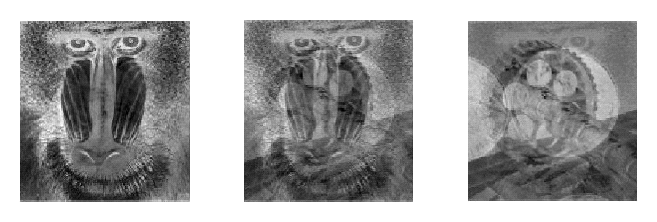

Mixed Signals

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

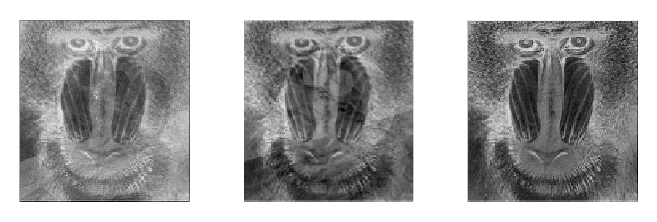

Mixes Correlation Matrix =  | Mix 1 | Mix 2 | Mix 3
Mix 1 | 1. | 0.47051 | 0.792735
Mix 2 | 0.47051 | 1. | 0.76425
Mix 3 | 0.792735 | 0.76425 | 1.

```mathematica
(*Input a desired mixing matrix (e.g. mixingSign[{{.4,.6},{.8,.2}}], for 2 sources) or the number of sources if you want a random mixing matrix (e.g. mixingSign[3], for 3 sources). Input an identity matrix of the desired size if no mixing is desired (e.g. mixingSign[IdentityMatrix[4]], for 4 sources)*)
{mix,nbCol}=mixingSign[3];
```

Performing ICA on mixed signals

```mathematica
Dimensions[mix]
```

{3,36864}

IC 1 computed in 5 steps

IC 2 computed in 6 steps

IC 3 computed in 1 steps

Extracted Components

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

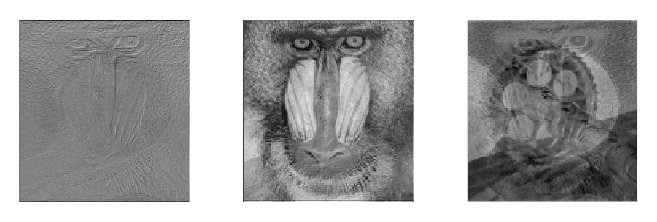

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

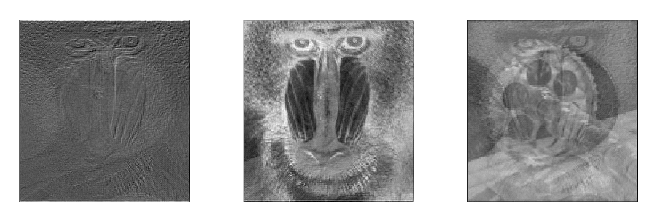

Independent Components Correlation Matrix=  | IC 1 | IC 2 | IC 3
IC 1 | 1. | 0 | 0
IC 2 | 0 | 1. | 0
IC 3 | 0 | 0 | 1.

{631.109,{«1»}}

```mathematica
ic=fastICA[mix,minDeltaW,maxStep,nbCol]//Timing
```